# Algorithm Overview

Trust region algorithms minimize f(x) by advancing from
	x_k→x_(k+1)=x_k+p
where p minimizes a typically quadratic model function 
	m[p]=g.p+0.5 p.A.p∼f[x_k+p]
 with g≈∇f(x_k) and A≈∇^2 f(x_k) over some trust region √(p.B.p)≤Δ.   Importantly if 
	f≈f(x_k)+g.p+0.5 p.A.p  for √(p.B.p)≤Δ 
and we find a reasonable solution of the TRS problem then x_(k+1) will improve on x_k.

Line-search algorithms choose a single direction p_k at x_k and looks for scalars α>0 for which 
	x_(k+1)=x_k+α p_k
improves x_k.  As before g≈∇f(x_k) and possibly A≈∇^2 f(x_k).  It is critical that p_k points downhill i.e.
	∇f(x_k).p_k<0.
Steepest descent is simply p_k=-∇f(x_k).  Newton like methods choose 
	p_k=-A^-1g
Unfortunately unless A is SPD this is a saddle.   Line search methods all need SPD A which is not great if ∇^2 f(x_k) is not SPD.

# Line Search

Lets look at a line search with the Rosenbrock function with n=9. First we are going to need some derivatives.

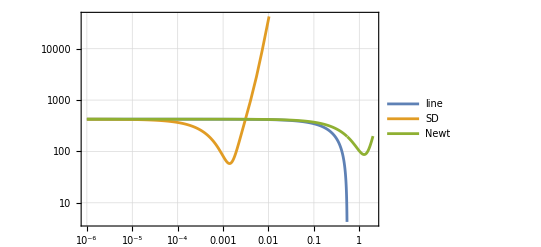

```mathematica
Rosen[x_List]:= Module[{n=Length[x],sum=0.0},
Do[
sum+=100.0(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,
{i,1,Length[x]-1}];
sum]
Clear[x,var]
n=9;
var=Array[x,n];
dRosen[x_]=Quiet[D[Rosen[var],{var}]/.x[i_]:>x⟦i⟧];
ddRosen[x_]=Quiet[D[Rosen[var],{var,2}]/.x[i_]:>x⟦i⟧];
x0=RandomReal[{-1,1},n];
{f0,g0,H0}={Rosen[x0],dRosen[x0],ddRosen[x0]};
pSD=-g0;
pNewt=-LinearSolve[H0,g0];
LogLogPlot[{f0-α Norm[g0],Rosen[x0+α pSD],Rosen[x0+α pNewt]},{α,10^-6, 2.0},PlotLegends->{"line","SD","Newt"},
GridLines->Automatic,Frame->True,
PlotRange->{0.01 f0, 100 f0}]
```